# Net Interval Constructions for Iterated Function Systems

## A symbolic computation and simulation library for iterated function systems satisfying a finite type condition.

Alex Rutar

Email: alex@rutar.org
Site: https://rutar.org

## Library Functions

## Weighted Iterated Function Systems

### Affine Function Constructions

We first define affine functions, which in our situation are simply functions f(x) = r x + d. In terms of implementation, it is useful for us to define two varieties: the first, which is just a symbol r x+d, while the second is a pair {rx+d, p} where p is some weight (in our situation, probabilities). When composing functions, it is also useful to keep track of the weights for future computations.

```mathematica
(* basic attributes *)
func[{aff:((_:1)*x+_:0),_}]:=aff
func[aff:((_:1)*x+_:0)]:=aff
prob[{(_:1)*x+_:0,pr_}]:=pr

(* contraction ratio *)
affineContraction[(r_:1)*x+_:0]:=r
affineContraction[{(r_:1)*x+_:0,_}]:=r

(* translation ratio *)
affineTranslation[(_:1)*x+d_:0]:=d
affineTranslation[{(_:1)*x+d_:0,_}]:=d

(* convert to a pure function for convenient calling *)
asPureFunction[(r_:1)*x+d_:0]:=r*#+d&
asPureFunction[{(r_:1)*x+d_:0,_}]:=r*#+d&

(* convenience evaluation functions *)
evalAtZero[(_:1)*x+d_:0]:=d
evalAtZero[{(_:1)*x+d_:0,_}]:=d
evalAtOne[(r_:1)*x+d_:0]:=r+d
evalAtOne[{(r_:1)*x+d_:0,_}]:=r+d

(* Inverse of the affine function (rasies divide by zero if constant) *)
affineInverse[(r_:1)*x+d_:0]:=x/r-d/r

(* Interval corresponding to the (p)aff *)
baseInterval:=Interval[{0,1}]
affineInterval[(r_:1)*x+d_:0]:=r*baseInterval+d
affineInterval[{(r_:1)*x+d_:0,_}]:=r*baseInterval+d
(* This is the affine map corresponding to the interval which satisfies f([0,1]) = iv *)
affineIntervalMap[Interval[{a_,b_}]]:=a+(b-a)*x

(* Composition rules for different variants of affine functions *)
affineCompose[(r1_:1)*x+d1_:0,(r2_:1)*x+d2_:0]:=r1*r2*x+r1*d2+d1
affineCompose[{(r1_:1)*x+d1_:0,p1_},{(r2_:1)*x+d2_:0,p2_}]:={r1*r2*x+r1*d2+d1,p1*p2}
affineCompose[(r1_:1)*x+d1_:0,{(r2_:1)*x+d2_:0,p2_}]:={r1*r2*x+r1*d2+d1,p2}
affineComposeList[aff_,afflist_]:=affineCompose[aff,#]&/@afflist

(* identifySameFunction collects elements in afflist together, and adding the corresponding probabilities. The variant with no probabilities simply deletes duplicate copies. *)
identifySameFunction[afflist_]:=DeleteDuplicates[afflist]
identifySameFunction[afflist_]:=KeyValueMap[{#1,#2}&,GroupBy[afflist,First->Last,Total]]
```

### Basics objects for WIFS

We now define objects which govern weighted iterated function systems, which are finite families of maps (f_i,p_i)_(i=1)^m, where each f_i(x)=r_i x+d_i is an affine function with 0<Abs[ri]<1 and p_i>0 with sum p_i=1. For our purposes, probabilityMap is any function which takes an index i and returns the corresponding probability p_i.

We also define the base notions of a net interval and a neighbour set. A neighbour set is simply a sorted list of unique affine functions (without probabilities), and a net interval is a {interval, neighbour set} pair.

```mathematica
weightedIFS[similarityList_,probabilityMap_]:=MapIndexed[{#1,probabilityMap@First[#2]}&,similarityList]
ConvexSupportQ[wifs_]:=IntervalUnion@@affineInterval/@wordToAffine[wifs,wordsOfLength[wifs,1]]===Interval[{0,1}]

(* the alphabet is just the set of indices {1, ..., m} *)
alphabet[wifs_]:=Range[Length[wifs]]

(* all possible words of length n on the alphabet *)
wordsOfLength[wifs_,n_]:=Tuples[alphabet[wifs],n]

(* get affine functions corresponding to words through wifs *)
(* convenience mappings which converts single words, or a list of words, into the corresponding affine functions (with probabilities) *)
wordToAffine[wifs_,word_]:=Fold[affineCompose,{x,1},wifs[[#]]&/@word]/;VectorQ[word,IntegerQ]
wordToAffine[wifs_,wordlist_]:=wordToAffine[wifs,#]&/@wordlist/;VectorQ[wordlist,ListQ]

baseNeighbourSet:={x}
baseNetInterval:={baseInterval,baseNeighbourSet}
```

## Constructing the Transition Graph

### General operations on Edge Tagged Graphs

```mathematica
listOutEdge[g_,v_]:=Cases[IncidenceList[g,v],v OverBar[->]_]
firstOutEdge[g_,v_]:=FirstCase[IncidenceList[g,v],v OverBar[->]_]
```

Here we enumerate all cycles of a given length in a general edge tagged graph g.

The function CyclesOfLength[g,n] returns an association with keys that are vertices in g and values a list of all paths (lists of edges) with length exactly n beginning and ending at that vertex. Note that this accounts for multiple edges and paths can repeat vertices or edges without issue. The function CyclesToLength[g,n] returns a list of all cycles in g with length at most n.

```mathematica
(* check if a path is a cycle *)
CycleQ[path:{(_ OverBar[->]_)..}]:=Switch[path,
{v_ OverBar[->] v_},True,
{v_ OverBar[->]_,___,_ OverBar[->] v_},True,
_,False
]
(* list of length 1 paths from vertex v to vertex w *)
singlePathsFrom[g_][v_,w_]:={#}&/@Cases[listOutEdge[g,v],v OverBar[->] w]
(* matrix where the i,j entry is a list of length 1 paths from the vertex with index i to the vertex with index j *)
edgeMatrix[g_]:=Outer[singlePathsFrom[g],VertexList[g],VertexList[g],1]
(* generalized inner product, except restricted to level 2 (for matrices) *)
level2Inner[f_,M1_,M2_,g_]:=Outer[g@@MapThread[f,{#1,#2}]&,M1,Transpose[M2],1]
allConcatenations[nestedList1_,nestedList2_]:=Flatten[Outer[Join,nestedList1,nestedList2,1],1]
CyclesOfLength[g_,n_]:=With[{M=edgeMatrix[g]},
Association@MapThread[
#1->#2&,
{VertexList[g],Diagonal@Nest[level2Inner[allConcatenations,M,#,Join]&,M,n-1]}
]
]

CyclesToLength[g_,n_]:=With[{M=edgeMatrix[g]},
Flatten[Diagonal/@NestList[level2Inner[allConcatenations,M,#,Join]&,M,n-1],2]
]
followToCycle[g_,edgeList:{___,lastEdge:_ OverBar[->] v_}]:=With[{nextEdge=firstOutEdge[g,v]},
If[First[edgeList]===nextEdge,
edgeList,
followToCycle[g,Append[edgeList,nextEdge]]]
]
SimpleLoopCycle[g_]:=followToCycle[g,{First@EdgeList[g]}]
```

### Computing the basic covering children of a neighbour set

Here we describe how to compute the children of net intervals. In fact, since the children depend only on the neighbour set, we actually define a type of “symbolic children” of our net interval, which allows the construction to be location invariant. The notion of children in this setting is therefore computed with respect to a neighbour set rather than a specific net interval. Note here that our children are with respect to covering neighbour sets: we do not check if f(K) ∩ (0,1) is non-empty. This will be resolved in the next section.

The children of a net interval are defined with respect to a fixed weighted IFS transition rule (which describes which neighbours to iterate in the neighbour set). A transition rule takes a list of affine functions, and returns a corresponding list of words of the same length.

```mathematica
(* given a list of affine functions, normalize them with respect to the interval iv (if the affine function does not have f([0,1]) containing iv, we simply ignore f from the list) *)
normalizeByInterval[iv:Interval[{_,_}],afflist_]:=affineComposeList[affineInverse[affineIntervalMap[iv]],Select[afflist,IntervalMemberQ[affineInterval[#],iv]&]]

(* using a transition rule and a weighted IFS, iterate on the neighbour set by composing on the right with all affine functions (with probabilities) corresponding to the sets of words given by the transition rule *)
neighbourSetTransitions[wifs_,transitionRule_,nbset_]:=MapThread[
{#1,identifySameFunction[affineComposeList[#1,wordToAffine[wifs,#2]]]}&,
{nbset,transitionRule[nbset]}]

(* given the transition functions, compute the child intervals (not including the neighbour sets, at this time) *)
childIntervals[transitions_]:=With[
{functions=Join@@Last/@transitions},
BlockMap[Interval[#]&,(* block map chunks the valid endpoints in pairs *)NumericalSort@DeleteDuplicates@Select[
Join[{0,1},evalAtZero/@functions,evalAtOne/@functions],(* all possible endpoints *)
IntervalMemberQ[baseInterval,#]& (* which are members of the interval [0,1] *)],
2,1]
]

(* for each net interval, create an association with keys given by the child intervals, and with values a substition rule converting valid pairs {parent nb, child nb} -> probability}} *)
childNeighbourPairAssociations[chivs_, transitions_]:=Association[Map[
Function[iv,iv->Association@Flatten@Map[Map[Function[aff,{#[[1]],func[aff]}->prob[aff]],normalizeByInterval[iv,#[[2]]]]&,transitions]],
chivs]]

(* assoc is a specific value associated with a gievn net interval *)

(* convert the association to a neighbour set *)
associationNbSet[assoc_]:=Union[Map[Last,Keys[assoc]]]

(* List of {position index, parent neighbour set, child neighbour set, transition matrix, edge weight} *)
basicChildEvaluator[wifs_,transitionRule_][nbset_]:=With[
{transitions = neighbourSetTransitions[wifs,transitionRule,nbset]},
With[{chivs = childIntervals[transitions]},
With[{assocs =childNeighbourPairAssociations[chivs,transitions]},
Select[Map[With[{childnbset = associationNbSet[assocs[#]]},{
Min[#], (* position index *)
nbset,
childnbset, (* child neighbour set *)
assocs[#], (* pair probabilities *)
Max[#]-Min[#]}]&, (* Edge weight *)
chivs],
Length[#[[3]]]> 0&]]]]
```

### Computing the covering transition graph

Now that we have a means of computing basic children, we obtain the (hopefully finite) transition graph by beginning with a vertex {x} and repeatedly computing expanding the graph by computing the children of vertices which have not yet been computed. If the WIFS is chosen well, we will end up with a finite graph (though, we typically do not know how long one would have to wait in order to compute the graph).

Since we want to allow multiple edges between vertices (distinguished by labels), our fundamental object here is the EdgeTaggedGraph. The vertex set of the graph is the set of all possible neighbour sets, and the edge set is given by the transitions between neighbour sets and their children, tagged with the position index. We also define some utility associations, which define mappings from edges in the transition graph to various attributes (the transition graph being the most notable).

```mathematica
(* compute an association with keys that are tagged edges with weights and values that are transition matrix *)
childVertices[children_]:=Replace[{_,_,chnbset_,_,_}:>chnbset]/@children
taggedEdges[children_]:=Replace[{posidx_,parnbset_,chnbset_,trmat_,eweight_}:>(parnbset(->)^posidx chnbset)-><|"Weight"->eweight,"Pair Probabilities"->trmat|>]/@children
(* iterates, returning a triple {computed vertices, iteration vertices, edge list} for repetition *)
(*allBasicChildRecursor[childEvaluator_,maxDepth_,taggedEdgeList_,computedVertices_,iterationVertices_]:=If[Echo[Length[computedVertices],"Computed: "]>maxDepth,*)
allBasicChildRecursor[childEvaluator_,maxDepth_,taggedEdgeList_,computedVertices_,iterationVertices_]:=If[Length[computedVertices]>maxDepth,
Throw["Exceeded maximum search depth!"],
If[Length[iterationVertices] == 0,
Association[taggedEdgeList],
With[{newChildren=childEvaluator/@iterationVertices},
With[
{newEdges=Union@@taggedEdges/@newChildren,
newVertices=Union@@childVertices/@newChildren},
allBasicChildRecursor[
childEvaluator,
maxDepth,
Union[newEdges,taggedEdgeList],
Union[computedVertices,newVertices],
Complement[newVertices,computedVertices]
]
]
]
]
]
(* the baseEdgeAssoc returns an association which takes edges and returns an association with keys "Weight" and "Pair Probabilities" *)
baseEdgeAssociation[{wifs_,transitionFunc_, _},maxDepth_]:=allBasicChildRecursor[basicChildEvaluator[wifs,transitionFunc[wifs]],maxDepth,{},{},{{x}}]
TransitionGraphFromEdgeAssociation[edgeAssoc_]:=EdgeTaggedGraph@Keys[edgeAssoc]
```

### Removing neighbours which are covering but not reduced

The base transition graph is computed with respect to covering neighbour sets. In order to restrict to the set of proper neighbour sets, we need to back-prune the graph in order to remove neighbours of net intervals which do not contribute to a child net interval. These neighbour sets correspond to rows such that every transition matrix of every outgoing edge is composed of all zeros, including after iteration. This function works with the “Pair Probabilities” element (which is an Association with Key-Value pairs {f_1,f_2}→p). By the nature of an IFS, if a neighbour f corresponds to a row of all zeros, this neighbour has f(K)∩(0,1)≠∅.

```mathematica
(* get neighbours corresponding to children with zeros for a given vertex *)
zeroNeighboursVertex[association_,trGraph_,vtx_]:=Select[vtx,FreeQ[Keys[association[#]["Pair Probabilities"]]&/@listOutEdge[trGraph,vtx],#,{3}]&]
(* get all neighbours corresponding to a zero *)
zeroNeighbours[association_,trGraph_]:=DeleteDuplicates[Flatten[zeroNeighboursVertex[association,trGraph,#]&/@VertexList[trGraph]]]

(* delete the entries in the pair probability elements and vertices corresponding to the unwanted neighbours *)
delNeighbourPairProbs[pairProbs_,nbList_]:=KeySelect[pairProbs,FreeQ[#,Alternatives@@nbList,{1}]&]
delNeighbourVertex[vtx_,nbList_]:=DeleteCases[vtx,Alternatives@@nbList]

(* return a new lookup pair for a given edge, with modified neighbour sets for vertices and modified pair probabilities *)
removeNbEdge[v_(->)^q_ w_,<|init___,"Pair Probabilities"->pairProbs_,end___|>,nbList_]:=delNeighbourVertex[v,nbList](->)^q delNeighbourVertex[w,nbList]-><|init,"Pair Probabilities"->delNeighbourPairProbs[pairProbs,nbList],end|>

(* now go through the association, apply the above transformation, and remove all the now empty vertex sets *)
emptyEdgeQ[v_ OverBar[->] w_]:=Not[v=={}||w=={}]
removeNeighbourList[association_,nbList_]:=KeySelect[
KeyValueMap[removeNbEdge[#1,#2,nbList]&,association],
emptyEdgeQ]

(* now construct the new transition graph by iterating the above process until there are no more transition matrices with rows of zero *)
removeFreeNeighbours[oldAssoc_]:=With[{oldGraph=TransitionGraphFromEdgeAssociation[oldAssoc]},
With[{zNbs=zeroNeighbours[oldAssoc,oldGraph]},
If[Length[zNbs]>0,
removeFreeNeighbours[removeNeighbourList[oldAssoc,zNbs]],
oldAssoc
]
]
]
```

### Computing the (proper) edge association

Finally, we define the edge association constructor, which builds the covering graph using the standard constructions and then uses the above reductions to get the proper transition graph. We also define some convenience functions which take edge associations and return various lookups on edges.

```mathematica
(* TODO options? contract edges *)
(* currently does not contract single edges *)
(* memoization: this is the main heavy computation EdgeAssociation[wifsTriple,maxDepth]= *)
EdgeAssociation[wifsTriple:{wifs_,transitionFunc_,uwFunc_},maxDepth_]:=With[{bEdge=baseEdgeAssociation[wifsTriple,maxDepth]},
If[ConvexSupportQ[wifs],
bEdge, (* if full support, never need to do any removal of neighbours *)
removeFreeNeighbours@bEdge
]
]
```

We also have a function which computes the transition graph given the edge association. Unlike its undecorated relative, this function also formats the graph nicely and assigns various visualization options (transition matrix and weight mouseover, etc.)

## Attributes and Analysis of the Transition Graph

### Converting probability pair associations to transition matrices and computing user weights

We now define functions designed to add transition matrices to the corresponding edge association.

```mathematica
pairLookup[association_,default_][e1_,e2_]:=With[{retval=association[{e1,e2}]},If[MissingQ[retval],default,retval]]
transitionMatrixRule[edge:v_w__,valAssoc_]:=edge->Outer[pairLookup[valAssoc["Pair Probabilities"],0],v,w]
TransitionMatrix[edgeAssoc_,edge_]:=edge/.transitionMatrixRule[edge,edgeAssoc[edge]]
TransitionMatrixAssociation[wifsTriple_,edgeAssoc_]:=Association[KeyValueMap[transitionMatrixRule,edgeAssoc]]
applyPair[uwFunc_][edge_,valAssoc_]:=edge->uwFunc[edge,valAssoc["Weight"]]
WeightAssociation[wifsTriple:{_,_,uwFunc_},edgeAssoc_]:=Association[KeyValueMap[applyPair[uwFunc],edgeAssoc]]
```

### Maximal loop classes and the essential class

A non-negative matrix M is irreducible if for each i,j, there exists some n such that (M^n)_(i,j)>0.

A loop class is simple if it is composed of a single loop - equivalently, the degree of every vertex is 2.

```mathematica
MaximalLoopClasses[graph_]:=Select[ConnectedGraphComponents[graph],EdgeCount[#]>0&]
EssentialClass[graph_]:=First@MaximalLoopClasses[graph]

neighbourConnectionList[v_ OverBar[->] w_,assocVal:<|___,"Pair Probabilities"->pprobs_,___|>]:={v,First[#]}->{w,Last[#]}&/@Keys[pprobs]
IrreducibleLoopQ[edgeAssoc_,loopClass_]:=ConnectedGraphQ@Graph@Flatten@KeyValueMap[neighbourConnectionList,KeyTake[edgeAssoc,EdgeList[loopClass]]]
SimpleLoopQ[edgeAssoc_,loopClass_]:=AllTrue[VertexDegree[loopClass],#===2&]
```

### Visualizing and Interacting with the Transition Graph

A maximal loop class is a strongly connected component such that for any vertices v and w, there is a non-empty path from v to w, such that the component is maximal with this property. Equivalently, it is a maximal strongly connected component with at least one edge. A maximal loop class is an essential class if it contains any vertex reachable from a path from a vertex in the maximal loop class.

```mathematica
trGraphInfo[wifsTriple:{_,_,uwAssoc_},edgeAssoc_,subgraph_]:=With[
{transitionAssoc=TransitionMatrixAssociation[wifsTriple,edgeAssoc],
weightAssoc=WeightAssociation[wifsTriple,edgeAssoc]},
EdgeTaggedGraph[subgraph,
VertexLabels->{v_:>Placed[{"Index",TableForm[v]},{Center,Tooltip}]},
EdgeLabels->Map[Function[edge,edge->Placed[TableForm[{EdgeIndex[subgraph,edge],MatrixForm@transitionAssoc[edge],weightAssoc[edge]},TableDirections->Row],Tooltip]],Keys[edgeAssoc]]
]
]
trGraphPlot[wifsTriple_,edgeAssoc_,subgraph_]:=GraphPlot[
HighlightGraph[subgraph,MaximalLoopClasses[subgraph]],
EdgeStyle->Opacity[0.3]]

Options[TransitionGraph]:={"Subgraph"->All,"Style"->"Plain"}
TransitionGraph[wifsTriple_,edgeAssoc_,OptionsPattern[]]:=With[{subgraph=If[OptionValue["Subgraph"]===All,TransitionGraphFromEdgeAssociation[edgeAssoc],OptionValue["Subgraph"]]},
Switch[OptionValue["Style"],
"Plain",subgraph,
"Index",With[{gr=EdgeTaggedGraph[subgraph,EdgeLabels->Placed["Index",Center],VertexLabels->Placed["Index",Center]]},HighlightGraph[gr,MaximalLoopClasses[gr]]],
"FullInfo", trGraphInfo[wifsTriple,edgeAssoc,subgraph],
"PlotOnly",trGraphPlot[wifsTriple,edgeAssoc,subgraph],
_,Throw["Invalid option!",OptionValue["Style"]]
]
]
```

### Operations on Graphs

We define functions used to compute the corresponding weights and transition matrices for paths. These functions are defined for paths specified as lists of edge objects or lists of edge indices.

```mathematica
PathWeight[weightAssoc_,path:{___,_ OverBar[->]_}]:=Times@@(weightAssoc[#]&/@path)
PathTransitionMatrix[transitionAssoc_,path:{___,_ OverBar[->]_}]:=Dot@@(transitionAssoc[#]&/@path)
PathWeight[weightAssoc_,path:{___,_Integer}]:=Times@@(weightAssoc[[#]]&/@path)
PathTransitionMatrix[transitionAssoc_,path:{___,_Integer}]:=Dot@@(transitionAssoc[[#]]&/@path)

LogPathWeight[weightAssoc_,path:{___,_ OverBar[->]_}]:=Total[Log/@(weightAssoc[#]&/@path)]
LogPathWeight[weightAssoc_,path:{___,_Integer}]:=Total[Log/@(weightAssoc[[#]]&/@path)]

(* convert a path in edges to a path as indices *)
PathAsIndex[edgeAssoc_,path_]:=EdgeIndex[TransitionGraphFromEdgeAssociation[edgeAssoc],#]&/@path
```

### Listing Information about Edges and Vertices

```mathematica
VertexIndexInfo[wifsTriple_,edgeAssoc_]:=With[{trg=TransitionGraphFromEdgeAssociation[edgeAssoc]},TableForm[({#1}&)/@VertexList[trg],TableHeadings->{Range[VertexCount[trg]],{"Neighbour Set"}},TableDepth->2]]
EdgePositionIndex[v_w_q_]:=q
EdgeIndexInfo[wifsTriple_,edgeAssoc_]:=With[{transitions=Values[TransitionMatrixAssociation[wifsTriple,edgeAssoc]],weights=Values[WeightAssociation[wifsTriple,edgeAssoc]],edges=Keys[edgeAssoc]},TableForm[MapThread[{#1,TraditionalForm[MatrixForm[#2]],EdgePositionIndex[#3]}&,{weights,transitions,edges}],TableHeadings->{Range[Length[edgeAssoc]],{"Edge Weight","Transition Matrix","Position Index"}}]]
WIFSInfo[wifsTriple_,edgeAssoc_]:=Row[{TransitionGraph[wifsTriple,edgeAssoc,"Style"->"Index"],VertexIndexInfo[wifsTriple,edgeAssoc],EdgeIndexInfo[wifsTriple,edgeAssoc]},Invisible["M"]]
```

### Contracting Single Edges

We now define a function which contracts edges corresponding to the unique child of some net interval. Note that this function assumes the transition matrices have been computed and added to the corresponding associations. This ensures that every vertex has at least two distinct children.

```mathematica
(* WARNING - currently broken *)
(* construct an edge corresponding to the path by combining position indices and edge weights properly. Assumes path is non-empty. Assumes the edges are in the corresponding association and actually form a path. Returns lookup edge -> {weight, matrix} *)
contractPathTail[assoc_,{},acc:(_ OverBar[->]_->{_,_})]:=acc
contractPathTail[assoc_,path:{___,edge1:v1_(->)^q1_ w1_},(edge2:v2_(->)^q2_ w2_)->eAssoc_]:=With[
{weight1=assoc[edge1]["Weight"]},
contractPathTail[assoc,Most[path],v1(->)^(q1+weight1*q2)w2-><|"Weight"->weight1*eAssoc["Weight"],"Transition Matrix"->Dot[assoc[edge1]["Transition Matrix"],eAssoc["Transition Matrix"]]|>]]
contractPath[assoc_,path_]:=contractPathTail[assoc,Most[path],Last[path]->assoc[Last[path]]]


(* starting with a path (sequence of edges), follow out degrees as far as possible (assumes no single self-loops) *)
followOutDegOne[g_,path:{___,_ OverBar[->] w_}]:=If[VertexOutDegree[g,w]==1,
followOutDegOne[g,Append[path,firstOutEdge[g,w]]],
path]

(* given an edge, when the source vertex has out degree > 1 and the target has out degree 1, return a rule taking as input the new edge and the {weight, matrix}. Otherwise, give the edge back *)
replaceEdge[g_,assoc_][edge:w_ OverBar[->] v_]:=If[VertexOutDegree[g,v]==1 && VertexOutDegree[g,w]>1,
contractPath[assoc,followOutDegOne[g,{edge}]],
edge->assoc[edge]
]

(* returns a pair consisting of the new transition graph as well as the new lookup *)
ContractSingleEdges[oldGraph_,oldAssoc_]:=With[
{tempAssoc=replaceEdge[oldGraph,oldAssoc]/@EdgeList[oldGraph]}, (* temporary rule transformation describing how to add joining edges *)
With[{newGraph=VertexDelete[EdgeTaggedGraph[Keys[tempAssoc]],_?(VertexOutDegree[oldGraph,#]==1&)]},
{newGraph,KeyTake[tempAssoc,EdgeList[newGraph]]}]]
```

### Investigating Sets of Local Dimensions

Here we define functions to compute the local dimension corresponding to a cycle.

```mathematica
(* spectral radius of a matrix *)
specRad[M_]:=Max@Abs@Eigenvalues[M]

assocCycleLocalDimensionPair[trAssoc_,weightAssoc_,path_]:={specRad@PathTransitionMatrix[trAssoc,path],PathWeight[weightAssoc,path]}
assocCycleLocalDimension[trAssoc_,weightAssoc_,path_]:=Log@specRad@PathTransitionMatrix[trAssoc,path]/LogPathWeight[weightAssoc,path]
CycleLocalDimension[wifsTriple_,edgeAssoc_,path_]:=assocCycleLocalDimension[TransitionMatrixAssociation[wifsTriple,edgeAssoc],WeightAssociation[wifsTriple,edgeAssoc],path]
```

Given a fixed edge weight and transition matrix, search for a path in the graph which has that exact edge weight and transition matrix.

```mathematica
(* LocalDimensionSearch[edgeAssoc_,loop_,{weight_,matrix_},powerDepth_,pathDepth_]:=List[NestList[{First[#]*weight,Last[#].matrix}&,{weight,matrix},powerDepth],
{PathWeight[edgeAssoc,#],PathTransitionMatrix[TransitionMatrixAssociation[edgeAssoc],#]}&/@CyclesToLength[loop,pathDepth]] *)
LocalDimensionPairs[wifsTriple_,edgeAssoc_,loop_,maxCycleLength_]:=With[
{trAssoc=TransitionMatrixAssociation[wifsTriple,edgeAssoc],
weightAssoc=WeightAssociation[wifsTriple,edgeAssoc]},
Join[{PathAsIndex[edgeAssoc,#]},assocCycleLocalDimensionPair[trAssoc,weightAssoc,#]]&/@CyclesToLength[loop,maxCycleLength]
]

FindExactRepeat[lst_]:=With[{rep=FindRepeat[lst]},
If[Mod[Length[lst],Length[rep]]==0,rep,lst]
]
LocalDimensions[trAssoc_,weightAssoc_,loop_,maxCycleLength_]:=
assocCycleLocalDimension[trAssoc,weightAssoc,#]&/@FindExactRepeat/@CyclesToLength[loop,maxCycleLength]

(* returns an interval contained in the set of local dimensions. Requires the probabilities to be defined. *)
InnerLocalDimensionBound[wifsTriple_,edgeAssoc_,loop_,maxCycleLength_]:=With[
{trAssoc=TransitionMatrixAssociation[wifsTriple,edgeAssoc],
weightAssoc=WeightAssociation[wifsTriple,edgeAssoc]},
Switch[loop,
_?(SimpleLoopQ[edgeAssoc,#]&),With[{dim=assocCycleLocalDimension[trAssoc,weightAssoc,SimpleLoopCycle[loop]]},Interval[{dim,dim}]],
_?(IrreducibleLoopQ[edgeAssoc,#]&),Interval@MinMax@LocalDimensions[trAssoc,weightAssoc,loop,maxCycleLength],
_,Throw["Loop must be simple or irreducible"]
]
]
```

## Families of Iterated Function Systems

### Constructor Functions

```mathematica
familyConstructor[wifs_,transitionFunc_,weightFunc_,probabilityList:{__}]:=familyConstructor[wifs,transitionFunc,weightFunc,Function[i,probabilityList[[i]]]]
familyConstructor[wifs_,transitionFunc_,weightFunc_,probabilityMap_]:={weightedIFS[wifs,probabilityMap],transitionFunc,weightFunc}
familyConstructor[wifs_,transitionFunc_,weightFunc_,"Uniform"]:=familyConstructor[wifs,transitionFunc,weightFunc,ConstantArray[1/Length[wifs],Length[wifs]]]
```

### Implemented Transition Functions and Weight Functions

#### Predefined Transition Functions

```mathematica
(* two standard predefined transition rules for convenience *)
RMax[afflist_]:=Max[(Abs@affineContraction[#])&/@afflist]
TransitionFunction["Uniform",n_][wifs_][afflist_]:=ConstantArray[wordsOfLength[wifs,n],Length[afflist]]
TransitionFunction["RMax"][wifs_][afflist_]:= 
If[Abs[affineContraction[#]]==RMax[afflist],wordsOfLength[wifs,1],wordsOfLength[wifs,0]]&/@afflist
```

#### Predefined User Weights

```mathematica
WeightFunction["Constant", c_][_,_]:=c
WeightFunction["TGRatio"][v_ OverBar[->] w_,weight_]:=weight*RMax[w]/RMax[v]
```

### Families of Weighted IFS

#### Inhomogeneous Examples

```mathematica
(* Requires ρ>0, r>0, ρ+2r-ρr<1 *)
WIFSFamily["LW04"][probabilityMap_,{ρ_,r_}]:=familyConstructor[
{ρ*x,r* x+ρ*(1-r),r*x+(1-r)},
TransitionFunction["RMax"],
WeightFunction["TGRatio"],
probabilityMap
]

(* Requires 0<r<1, 0<ρ<1, r^2>ρ, ρ(r-1)(r+ρ-1)>r^2 *)
WIFSFamily["DN12"][probabilityMap_,{ρ_,r_}]:=familyConstructor[
{
{ρ*x,r*x+ρ*(1-r),(r^2/ρ)*x+(1-r)*(ρ+r),r*x+1-r},
TransitionFunction["Uniform",1],
WeightFunction["TGRatio"]
},
probabilityMap
]

(* Requires 0 < a ≤ Root[2#^2+3#-1&,2] *)
WIFSFamily["Rut21a"][probabilityMap_,a_]:=With[{b=a/(1+a)},familyConstructor[
{a*x,b*x+a*b,a*x+1-2*b,b*x+(1-b)},
TransitionFunction["RMax"],
WeightFunction["TGRatio"],
probabilityMap
]]

(* Requires 0 < a ≤ Root[#^2+#-1&,2] *)
WIFSFamily["Rut21b"][probabilityMap_,a_]:=With[{b=a/(1+a)},familyConstructor[
{a*x,b*x+a*b,b*x+(1-b)},
TransitionFunction["RMax"],
WeightFunction["TGRatio"],
probabilityMap]
]
```

#### Bernoulli Convolutions

Bernoulli convolutions are finite type if and only if the associated contractions are reciprocals of Pisot numbers (real algebraic integers strictly greater than one, with Galois conjugates having modulus strictly less than one). A special case of a Pisot number is a simple Pisot number, which is the unique positive real root of the polynomial x^k-(x^(k-1)+x^(k-2)+...+x+1) for k≥2.

```mathematica
WIFSFamily["BernoulliConvolution"][probabilityMap_,λ_]:=familyConstructor[
{λ*x,λ*x+(1-λ)},
TransitionFunction["Uniform",1],
WeightFunction["Constant",λ],
probabilityMap]

WIFSFamily["SimplePisotBernoulliConvolution"][probabilityMap_,n_]:=WIFSFamily["BernoulliConvolution"][probabilityMap,SimplePisotReciprocal[n]]
WIFSFamily["TwofoldBernoulliConvolution"][probabilityMap_,λ_]:=familyConstructor[
{λ*x,λ*x+λ/2-1/2,λ*x+(1-λ)},
TransitionFunction["Uniform",1],
WeightFunction["Constant",λ],
probabilityMap]
(* get the reciprocal pisot number given the minimal polynomial as a pure function *)
pisotReciprocal[poly_]:=With[{symb=Unique[]},
AlgebraicNumber[1/(First@MaximalBy[(symb/.#)&/@Solve[poly[symb]==0,symb],Abs]),{0,1}]
]
SimplePisotReciprocal[n_]:=pisotReciprocal[Function[t,t^n-Total[t^(#-1)&/@Range[n]]]]



(* A list of the first 10 largest reciprocals of Pisot numbers, in descending order *)
LargestPisotReciprocals:=pisotReciprocal/@{
#^3-#-1&, (* 1809 vertices, 5 non-essential: irreducible: {T,F,F,T,T}, simple: {T,T,T,T,T} *)
#^4-#^3-1&, (* ≥ 117 477 vertices ... *)
#^5-#^4-#^3+#^2-1&, (* ≥ 10 000 vertices ... *)
#^3-#^2-1&, (* 152 vertices, 4 non-essential: irreducible: {T,T,T,T}, simple: {F,T,T,T} *)
#^6-#^5-#^4+#^2-1&, (* ≥ 10 000 vertices ... *)
#^5-#^3-#^2-#-1&, (* ≥ 10 000 vertices ... *)
#^7-#^6-#^5+#^2-1&, (* ≥ 10 000 vertices ... *)
#^6-2#^5+#^4-#^2+#-1&, (* ≥ 10 000 vertices ... *)
#^5-#^4-#^2-1&, (* ≥ 10 000 vertices ... *)
#^8-#^7-#^6+#^2-1&  (* ≥ 5 000 vertices ... *)
}

(* A list of pisot reciprocals from the paper HHM2016 not included in the above lists *)
HHM16PisotReciprocals:=pisotReciprocal/@{
-1+#1-2 #1^2+#1^3&, (* 30 vertices, 2 non-essential: irreducible: {T,T}, simple: {T,T} *)
1-2 #1^2-#1^3+#1^4&,(* 538 vertices, 2 non-essential: irreducible: {T,T}, simple: {T,T} *)
-1+#1-2 #1^3+#1^4&, (* 190 vertices, 2 non-essential: irreducible: {T,T}, simple: {T,T} *)
-1-#1-#1^2-#1^3+#1^4& (* 14 vertices, 2 non-essential: irreducible: {T,T}, simple: {T,T} *)
}
```

#### A Family of Examples of Testud

```mathematica
WIFSFamily["Tes06"][probabilityMap_,{posList_,negList_}]:=With[{lmax=Max@Abs[posList~Join~negList]+1},familyConstructor[
Join[(1/lmax)*x+#/lmax&/@posList,(-1/lmax)*x+(#+1)/lmax&/@negList],
TransitionFunction["Uniform",1],
WeightFunction["Constant",1/lmax],
probabilityMap]
]
```

#### Cantor-Like Measures

```mathematica
WIFSFamily["UniformCantor"][probabilityMap_,{m_,r_}]:=familyConstructor[
(x/r+#(r-1)/(m r))&/@Range[0,m],
TransitionFunction["Uniform",1],
WeightFunction["Constant",1/r],
probabilityMap
]
WIFSFamily["ArbitraryCantor"][probabilityMap_,{contractionRatio_,shiftRatio_,shiftList_}]:=familyConstructor[
(contractionRatio*x+shiftRatio*#)&/@shiftList,
TransitionFunction["Uniform",1],
WeightFunction["Constant",contractionRatio],
probabilityMap
]
```

#### Inhomogenous Finite Type

```mathematica
(* requires a ≤ (sqrt(5)-1)/2*)
WIFSFamily["Rut21c"][probabilityMap_,a_]:=With[{b=a/(1+a)},familyConstructor[
{a*x,b*x+a *b,b*x+1-b},
TransitionFunction["RMax"],
WeightFunction["TGRatio"],
probabilityMap
]
]
```

## Some Example Usage

First we define a weighted IFS, which is the Bernoulli convolution associated with the reciprocal of the Golden mean, along with a transition rule for that IFS. We then compute its transition graph. The set of possible neighbour sets is precisely the vertex set of the transition graph.

```mathematica
ClearAll[p];
p[1]=p;p[2]=1-p;
wifsTriple=WIFSFamily["SimplePisotBernoulliConvolution"][p,2];
eassoc=EdgeAssociation[wifsTriple,100000];
trGraph=TransitionGraph[wifsTriple,eassoc]
```

-Graphics-

We can highlight the maximal loop classes of the transition graph. The maximal loop classes are the maximal strongly connected components which contain at least one edge. As can be seen in the below diagram, there are three: the red essential class, and two simple loops.

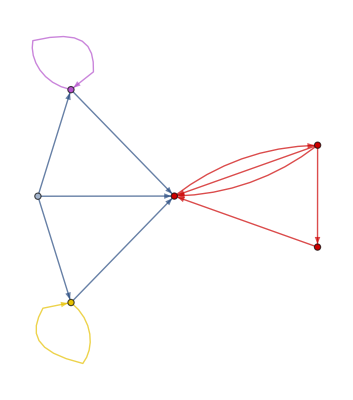

```mathematica
HighlightGraph[trGraph,MaximalLoopClasses[trGraph]]
```

The transition graph by itself is nice, but often it is more convenient to print out information about the IFS in a human-readable form. Below, the vertex labels correspond to the neighbour sets and the relevant information about the edge labels is given in the second table.

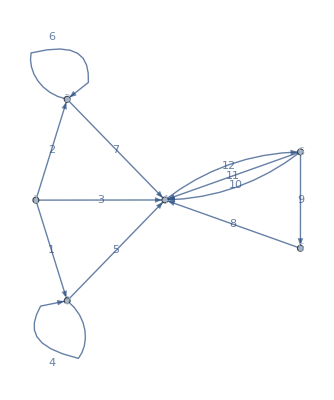
-Graphics-M | Neighbour Set
1 | {x}
2 | {x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895}
3 | {AlgebraicNumber-0.618AlgebraicNumber[1/2 (-1+√5),{0,-1}]-0.6180339887498949+x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895}
4 | {x AlgebraicNumber2.62AlgebraicNumber[1/2 (-1+√5),{2,1}]2.618033988749895,AlgebraicNumber-1.62AlgebraicNumber[1/2 (-1+√5),{-1,-1}]-1.618033988749895+x AlgebraicNumber2.62AlgebraicNumber[1/2 (-1+√5),{2,1}]2.618033988749895}
5 | {AlgebraicNumber-1.62AlgebraicNumber[1/2 (-1+√5),{-1,-1}]-1.618033988749895+x AlgebraicNumber4.24AlgebraicNumber[1/2 (-1+√5),{3,2}]4.23606797749979}
6 | {x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895,AlgebraicNumber-0.618AlgebraicNumber[1/2 (-1+√5),{0,-1}]-0.6180339887498949+x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895}M | Edge Weight | Transition Matrix | Position Index
1 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p) | 0
2 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p) | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949
3 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | AlgebraicNumber0.382AlgebraicNumber[1/2 (-1+√5),{1,-1}]0.3819660112501051
4 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p) | 0
5 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949
6 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p) | AlgebraicNumber0.382AlgebraicNumber[1/2 (-1+√5),{1,-1}]0.3819660112501051
7 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | 0
8 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | 0
9 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p
1-p) | AlgebraicNumber0.382AlgebraicNumber[1/2 (-1+√5),{1,-1}]0.3819660112501051
10 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p | 0
1-p | p) | 0
11 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p
0 | 1-p) | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949
12 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p | 0
0 | 1-p) | 0

```mathematica
WIFSInfo[wifsTriple,eassoc]
```

## Code for “Local Dimensions of Measures satisfying the Finite Neighbour Condition”

## Bernoulli Convolutions

```mathematica
ClearAll[p];
p[1]=p;p[2]=1-p;
wifsTriple=WIFSFamily["SimplePisotBernoulliConvolution"][p,2];
eassoc=EdgeAssociation[wifsTriple,100000];
WIFSInfo[wifsTriple,eassoc]
```

-Graphics-M | Neighbour Set
1 | {x}
2 | {x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895}
3 | {AlgebraicNumber-0.618AlgebraicNumber[1/2 (-1+√5),{0,-1}]-0.6180339887498949+x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895}
4 | {x AlgebraicNumber2.62AlgebraicNumber[1/2 (-1+√5),{2,1}]2.618033988749895,AlgebraicNumber-1.62AlgebraicNumber[1/2 (-1+√5),{-1,-1}]-1.618033988749895+x AlgebraicNumber2.62AlgebraicNumber[1/2 (-1+√5),{2,1}]2.618033988749895}
5 | {AlgebraicNumber-1.62AlgebraicNumber[1/2 (-1+√5),{-1,-1}]-1.618033988749895+x AlgebraicNumber4.24AlgebraicNumber[1/2 (-1+√5),{3,2}]4.23606797749979}
6 | {x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895,AlgebraicNumber-0.618AlgebraicNumber[1/2 (-1+√5),{0,-1}]-0.6180339887498949+x AlgebraicNumber1.62AlgebraicNumber[1/2 (-1+√5),{1,1}]1.618033988749895}M | Edge Weight | Transition Matrix | Position Index
1 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p) | 0
2 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p) | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949
3 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | AlgebraicNumber0.382AlgebraicNumber[1/2 (-1+√5),{1,-1}]0.3819660112501051
4 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p) | 0
5 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949
6 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p) | AlgebraicNumber0.382AlgebraicNumber[1/2 (-1+√5),{1,-1}]0.3819660112501051
7 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | 0
8 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p) | 0
9 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p
1-p) | AlgebraicNumber0.382AlgebraicNumber[1/2 (-1+√5),{1,-1}]0.3819660112501051
10 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p | 0
1-p | p) | 0
11 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (1-p | p
0 | 1-p) | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949
12 | AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949 | (p | 0
0 | 1-p) | 0

```mathematica
Assuming[1/2<p<1,Simplify[CycleLocalDimension[wifsTriple,eassoc,{10,12}]]]
Assuming[0<p<1/2,Simplify[CycleLocalDimension[wifsTriple,eassoc,{11,12}]]]
```

Log[p]/Log[AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949]

Log[(-1+p)^2]/(2 Log[AlgebraicNumber0.618AlgebraicNumber[1/2 (-1+√5),{0,1}]0.6180339887498949])

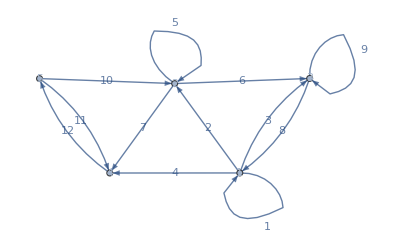
-Graphics-M | Neighbour Set
1 | {x}
2 | {(4 x)/3}
3 | {-1/2+(3 x)/2}
4 | {3 x,-3+4 x}
5 | {x,3 x}M | Edge Weight | Transition Matrix | Position Index
1 | 1/4 | (p(3)) | 3/4
2 | 1/3 | (p) | 0
3 | 1/4 | (1-p) | 1/3
4 | 1/3 | (1-p | p) | 1/4
5 | 1/3 | (p) | 0
6 | 1/4 | (1-p) | 4/9
7 | 1/3 | (1-p | p) | 1/3
8 | 1/4 | (p(3)) | 5/8
9 | 1/4 | (1-p) | 0
10 | 1/3 | (1
p) | 0
11 | 1/3 | (0 | 1
1-p | p) | 3/4
12 | 3/4 | (0 | 1
p(3) | 0) | 0

```mathematica
ClearAll[p];
p[1]=p;p[2]=1-p;
wifsTriple=WIFSFamily["LW04"][p,{1/3,1/4}];
eassoc=EdgeAssociation[wifsTriple,100000];
WIFSInfo[wifsTriple,eassoc]
```

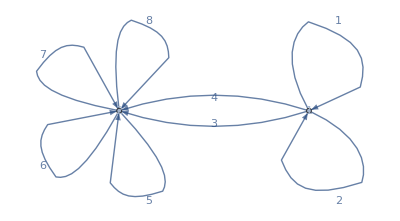
-Graphics-M | Neighbour Set
1 | {x}
2 | {1-x,x}M | Edge Weight | Transition Matrix | Position Index
1 | 1/4 | (p_3) | 1/2
2 | 1/4 | (p_4) | 3/4
3 | 1/4 | (p_5 | p_1) | 0
4 | 1/4 | (p_6 | p_2) | 1/4
5 | 1/4 | (p_4 | 0
p_5 | p_1) | 0
6 | 1/4 | (p_3 | 0
p_6 | p_2) | 1/4
7 | 1/4 | (p_2 | p_6
0 | p_3) | 1/2
8 | 1/4 | (p_1 | p_5
0 | p_4) | 3/4

```mathematica
ClearAll[p];
p[i_]:=Subscript[p,i];
wifsTriple=WIFSFamily["Tes06"][p,{{0,1,2,3},{0,1}}];
eassoc=EdgeAssociation[wifsTriple,100000];
WIFSInfo[wifsTriple,eassoc]
```

```mathematica
trAssoc=TransitionMatrixAssociation[wifsTriple,eassoc]
```

<|{x}{x}1/2→{{p[3]}},{x}{x}3/4→{{p[4]}},{x}{1-x,x}0→{{p[5],p}},{x}{1-x,x}1/4→{{p[6],1-p}},{1-x,x}{1-x,x}0→{{p[4],0},{p[5],p}},{1-x,x}{1-x,x}1/4→{{p[3],0},{p[6],1-p}},{1-x,x}{1-x,x}1/2→{{1-p,p[6]},{0,p[3]}},{1-x,x}{1-x,x}3/4→{{p,p[5]},{0,p[4]}}|>

```mathematica
PathTransitionMatrix[trAssoc,{7,6}]
```

{{(1-p) p_3+p_6^2,(1-p) p_6},{p_3 p_6,(1-p) p_3}}

## Testing

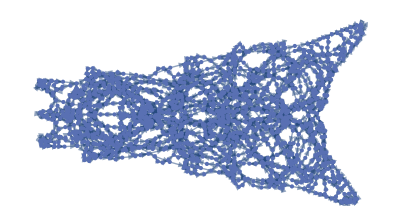

```mathematica
ClearAll[p];
p[i_]:=Subscript[p,i]
wifsTriple=WIFSFamily["BernoulliConvolution"][p,LargestPisotReciprocals[[1]]];
eassoc=EdgeAssociation[wifsTriple,10000];
trGraph=TransitionGraph[wifsTriple,eassoc]
```

```mathematica
IrreducibleLoopQ[eassoc,#]&/@MaximalLoopClasses@trGraph
```

{True,True,False,False,True,True}

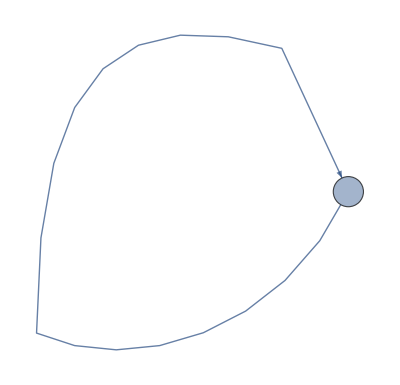

-Graphics-

```mathematica
nIrred1=MaximalLoopClasses[trGraph][[3]]
nIrred2=MaximalLoopClasses[trGraph][[4]]
```

```mathematica
AdjacencyGraph@Map[If[#===0,0,1]&,TransitionMatrix[eassoc,EdgeList[nIrred2][[1]]],{2}]
```

-Graphics-

```mathematica
TransitionMatrix[eassoc,EdgeList[nIrred2][[1]]]//MatrixForm
```

(p_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | p_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | p_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | p_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
p_1 | 0 | 0 | 0 | 0 | p_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | p_1 | 0 | 0 | 0 | 0 | p_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | p_1 | 0 | 0 | p_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | p_1 | 0 | 0 | p_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | p_1 | 0 | 0 | 0 | 0 | p_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | p_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | p_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | p_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | p_1 | 0)